```mathematica
α := 1/0.1
```

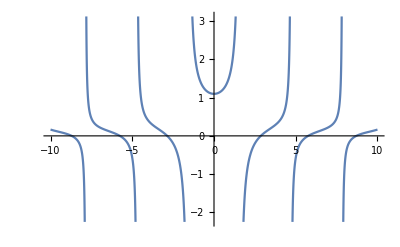

```mathematica
Plot[(Tan[x]/x)  +1/α,{x,-10,10}]
```

```mathematica
L[1]=FindRoot[Tan[x]/x+1/α==0,{x,π}]
L[2]=FindRoot[Tan[x]/x+1/α==0,{x,2π}]
L[3]=FindRoot[Tan[x]/x+1/α==0,{x,3π}]
L[4]=FindRoot[Tan[x]/x+1/α==0,{x,4π}]
L[5]=FindRoot[Tan[x]/x+1/α==0,{x,5π}]
L[6]=FindRoot[Tan[x]/x+1/α==0,{x,6π}]
L[7]=FindRoot[Tan[x]/x+1/α==0,{x,7π}]
L[8]=FindRoot[Tan[x]/x+1/α==0,{x,8π}]
L[9]=FindRoot[Tan[x]/x+1/α==0,{x,9π}]
L[10]=FindRoot[Tan[x]/x+1/α==0,{x, 10π}]
L[11]=FindRoot[Tan[x]/x+1/α==0,{x,11π}]
```

{x→2.86277}

{x→5.76056}

{x→8.70831}

{x→11.7027}

{x→14.7335}

{x→17.7908}

{x→20.8672}

{x→23.9574}

{x→27.0576}

{x→30.1652}

{x→30.1652}

```mathematica
F[y_,t_]:=-2/(1+α)∑_(n=1)^10 Exp[-L[n]^2 t]*(L[n]Tan[L[n]/2]+1/0.1(L[n]Csc[L[n]]-1))/((L[n]Csc[L[n]])^2+α)(Cos[L[n]y]-Cot[L[n]]Sin[L[n]y])
```

```mathematica
Plot[(1+y/1)/(1+1/1)+F[y,0.2],{y,0,1}]
```

-Graphics-

```mathematica
∫_0^1 (1+α z)(Cos[λ z]-Cot[λ]Sin[λ z])ⅆz
```

(-α+α λ Csc[λ]+λ Tan[λ/2])/λ^2

```mathematica
∫_0^1 (Cos[β z]-Cot[β]Sin[β z])(Cos[λ z]-Cot[λ]Sin[λ z])ⅆz
```

(-β Cot[β]+λ Cot[λ])/(β^2-λ^2)

```mathematica
∫_0^1 (Cos[λ z]-Cot[λ]Sin[λ z])^2 ⅆz
```

-(Cot[λ]-λ Csc[λ]^2)/(2 λ)

```mathematica
A= - 1/(∫_0^1 (Cos[λ z]-Cot[λ]Sin[λ z])^2 ⅆz) ∫_0^1 ( (1+α z)/(1 + α) )(Cos[λ z]-Cot[λ]Sin[λ z])ⅆz
```

```mathematica
(2 (-α+α λ Csc[λ]+λ Tan[λ/2]))/((1+α) λ (Cot[λ]-λ Csc[λ]^2))
```

(0.181818 (-10.+10. λ Csc[λ]+λ Tan[λ/2]))/(λ (Cot[λ]-λ Csc[λ]^2))

```mathematica
F[y_,t_]:=∑_(n=1)^10 Exp[-L[n]^2 t]*(2 (-α+α λ Csc[λ]+λ Tan[λ/2]))/((1+α) λ (Cot[λ]-λ Csc[λ]^2))*(Cos[L[n]y]-Cot[L[n]]Sin[L[n]y])
Plot[(1+α y)/(1+α)+F[y,0.2],{y,0,1}]
```

-Graphics-

-Graphics-